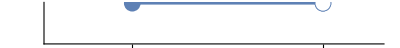

```mathematica
SetDirectory[NotebookDirectory[]];
NumberLinePlot[-5<=x<2,x,PlotRange->{-8,4},Ticks->{{-5,2}},PlotStyle->{Thickness[0.005],PointSize[0.03]},AxesLabel->HoldForm[Reals],Spacings->1,AxesStyle->Directive[16]]
Export["m5-2.svg",%];
Export["m5-2.pdf",%%];
```

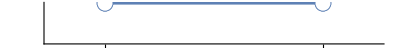

ab1.svg

ab1.pdf

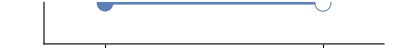

ab2.svg

ab2.pdf

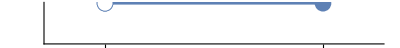

ab3.svg

ab3.pdf

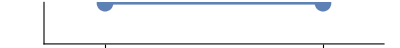

ab4.svg

ab4.pdf

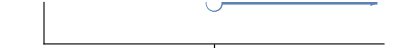

ab5.svg

ab5.pdf

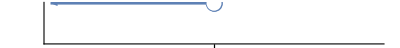

ab6.svg

ab6.pdf

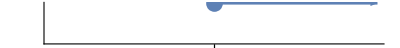

ab7.svg

ab7.pdf

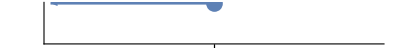

ab8.svg

ab8.pdf

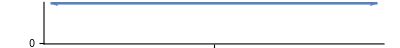

ab9.svg

ab9.pdf

```mathematica
a=-1;
b=3;
NumberLinePlot[a<x<b,x,PlotRange->{a-1,b+1},Ticks->{{{a,HoldForm[TraditionalForm[a]]},{b,HoldForm[TraditionalForm[b]]}}},PlotStyle->{Thickness[0.005],PointSize[0.03]},AxesLabel->HoldForm[Reals],Spacings->1,AxesStyle->Directive[16]]
Export["ab1.svg",%]
Export["ab1.pdf",%%]
NumberLinePlot[a<=x<b,x,PlotRange->{a-1,b+1},Ticks->{{{a,HoldForm[TraditionalForm[a]]},{b,HoldForm[TraditionalForm[b]]}}},PlotStyle->{Thickness[0.005],PointSize[0.03]},AxesLabel->HoldForm[Reals],Spacings->1,AxesStyle->Directive[16]]
Export["ab2.svg",%]
Export["ab2.pdf",%%]
NumberLinePlot[a<x<=b,x,PlotRange->{a-1,b+1},Ticks->{{{a,HoldForm[TraditionalForm[a]]},{b,HoldForm[TraditionalForm[b]]}}},PlotStyle->{Thickness[0.005],PointSize[0.03]},AxesLabel->HoldForm[Reals],Spacings->1,AxesStyle->Directive[16]]
Export["ab3.svg",%]
Export["ab3.pdf",%%]
NumberLinePlot[a<=x<=b,x,PlotRange->{a-1,b+1},Ticks->{{{a,HoldForm[TraditionalForm[a]]},{b,HoldForm[TraditionalForm[b]]}}},PlotStyle->{Thickness[0.005],PointSize[0.03]},AxesLabel->HoldForm[Reals],Spacings->1,AxesStyle->Directive[16]]
Export["ab4.svg",%]
Export["ab4.pdf",%%]
NumberLinePlot[a<x,x,PlotRange->All,Ticks->{{{a,HoldForm[TraditionalForm[a]]},{a,HoldForm[TraditionalForm[a]]}}},PlotStyle->{Thickness[0.005],PointSize[0.03]},AxesLabel->HoldForm[Reals],Spacings->1,AxesStyle->Directive[16]]
Export["ab5.svg",%]
Export["ab5.pdf",%%]
NumberLinePlot[x<a,x,PlotRange->All,Ticks->{{{a,HoldForm[TraditionalForm[a]]},{a,HoldForm[TraditionalForm[a]]}}},PlotStyle->{Thickness[0.005],PointSize[0.03]},AxesLabel->HoldForm[Reals],Spacings->1,AxesStyle->Directive[16]]
Export["ab6.svg",%]
Export["ab6.pdf",%%]
NumberLinePlot[a<=x,x,PlotRange->All,Ticks->{{{a,HoldForm[TraditionalForm[a]]},{a,HoldForm[TraditionalForm[a]]}}},PlotStyle->{Thickness[0.005],PointSize[0.03]},AxesLabel->HoldForm[Reals],Spacings->1,AxesStyle->Directive[16]]
Export["ab7.svg",%]
Export["ab7.pdf",%%]
NumberLinePlot[x<=a,x,PlotRange->All,Ticks->{{{a,HoldForm[TraditionalForm[a]]},{a,HoldForm[TraditionalForm[a]]}}},PlotStyle->{Thickness[0.005],PointSize[0.03]},AxesLabel->HoldForm[Reals],Spacings->1,AxesStyle->Directive[16]]
Export["ab8.svg",%]
Export["ab8.pdf",%%]
NumberLinePlot[True,x,PlotRange->All,Ticks->{{0}},PlotStyle->{Thickness[0.005],PointSize[0.03]},AxesLabel->HoldForm[Reals],Spacings->1,AxesStyle->Directive[16]]
Export["ab9.svg",%]
Export["ab9.pdf",%%]
```

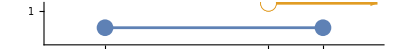

union1.svg

union1.pdf

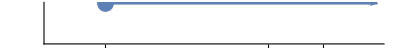

union2.svg

union2.pdf

```mathematica
NumberLinePlot[
{-3<=x<=1,0<x},x,PlotRange->{-4,2},Ticks->
{{-3,0,1}},PlotStyle->{{Thickness[0.005],PointSize[0.03]}},AxesLabel->HoldForm[Reals],Spacings->{0.5,0.75},AxesStyle->Directive[16],PlotRangePadding->1]
Export["union1.svg",%]
Export["union1.pdf",%%]
NumberLinePlot[
{-3<=x},x,PlotRange->{-4,2},Ticks->
{{-3,0,1}},PlotStyle->{{Thickness[0.005],PointSize[0.03]}},AxesLabel->HoldForm[Reals],PlotRangePadding->1,Spacings->0.5,AxesStyle->Directive[16]]
Export["union2.svg",%]
Export["union2.pdf",%%]
```

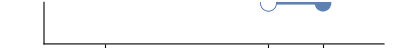

intersection.svg

intersection.pdf

```mathematica
NumberLinePlot[
{0<x<=1},x,PlotRange->{-4,2},Ticks->
{{-3,0,1}},PlotStyle->{{Thickness[0.005],PointSize[0.03]}},AxesLabel->HoldForm[Reals],PlotRangePadding->1,Spacings->0.75,AxesStyle->Directive[16]]
Export["intersection.svg",%]
Export["intersection.pdf",%%]
```

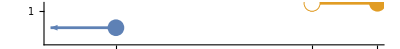

intersection2.svg

intersection2.pdf

```mathematica
NumberLinePlot[
{x<=-3,0<x<=1},x,PlotRange->{-4,All},Ticks->
{{-3,0,1}},PlotStyle->{{Thickness[0.005],PointSize[0.03]}},AxesLabel->HoldForm[Reals],Spacings->{0.5,0.75},AxesStyle->Directive[16]]
Export["intersection2.svg",%]
Export["intersection2.pdf",%%]
```

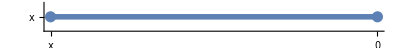

absolute.svg

absolute.pdf

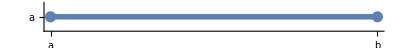

distance.svg

distance.pdf

```mathematica
a=0;
b=3;
NumberLinePlot[a<=x<=b,x,PlotRange->{a-1,b+1},Ticks->{{{a,HoldForm[TraditionalForm[x]]},{b,HoldForm[TraditionalForm[0]]}}},PlotStyle->{Thickness[0.01],PointSize[0.02]},AxesLabel->HoldForm[Reals],Spacings->0,AxesStyle->Directive[16],Epilog->{Inset[Style[HoldForm[Abs[x]],18],{b/2,-2}]}]
Export["absolute.svg",%]
Export["absolute.pdf",%%]
a=0;
b=3;
NumberLinePlot[a<=x<=b,x,PlotRange->{a-1,b+1},Ticks->{{{a,HoldForm[TraditionalForm[a]]},{b,HoldForm[TraditionalForm[b]]}}},PlotStyle->{Thickness[0.01],PointSize[0.02]},AxesLabel->HoldForm[Reals],Spacings->0,AxesStyle->Directive[16],Epilog->{Inset[Style[HoldForm[Abs[a-b]],18],{b/2,-2}]}]
Export["distance.svg",%]
Export["distance.pdf",%%]
```